# Spectral Lags in Very High Energy Emission of GRBs

## Numerical functions findRoot

Only works for monotonously increasing functions, which have a root for var > 0

```mathematica
findRoot[func_,{var_,start_?NumericQ}]:=Block[{left,right},
If[(func/.var->start)<0,
left=start;
right=2.start;
While[(func/.var->right)<0,right*=2;left*=2];
,
right=start;
left=.5start;
While[(func/.var->left)>0,left*=.5;right*=.5];
];
FindRoot[func,{var,left,right}]
]
```

## Model

### Parameters

```mathematica
universe={Hobs_,Ωm_};
```

```mathematica
population={density0_,index_,zc_};
```

```mathematica
burst={γ_,η0_,r0_,n_,ω0_,θ0_,k_,α_};
```

```mathematica
observer={detectorArea_,z_,χ_};
```

```mathematica
Options[defaultUniverse]={Hobs->2.*^-18,Ωm->0.317};
defaultUniverse[OptionsPattern[]]:={OptionValue[Hobs],OptionValue[Ωm]};
```

```mathematica
Options[defaultPopulation]={density0->0.655427*^-50,index->3,zc->3.};
defaultPopulation[OptionsPattern[]]:={OptionValue[density0],OptionValue[index],OptionValue[zc]};
```

```mathematica
Options[defaultBurst]={γ->100.,η0->1.*^45,r0->2.*^3,n->6,ω0->1.,θ0->2.5*^-5,k->-1,α->-1};
defaultBurst[OptionsPattern[]]:={OptionValue[γ],OptionValue[η0],OptionValue[r0],OptionValue[n],OptionValue[ω0],OptionValue[θ0],OptionValue[k],OptionValue[α]};
```

```mathematica
defaultDetectorArea[]:=5.563*^-18;
```

```mathematica
Options[defaultObserver]={detectorArea->defaultDetectorArea[],z->1.,χ->0.};
defaultObserver[OptionsPattern[]]={OptionValue[detectorArea],OptionValue[z],OptionValue[χ]};
```

### Relativity

```mathematica
v[γ_]:=√(1-1/γ^2);
```

### Cosmology

```mathematica
ΩΛ[Ωm_]:=1-Ωm;
```

```mathematica
distance[universe,z_]:=1/Hobs √(1/ΩΛ[Ωm])((1+z)Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm](1+z)^3]-Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm]]);
```

```mathematica
photonSphereArea[universe_,z_]:=4π distance[universe,z]^2;
```

```mathematica
burstsSphereArea[universe_,z_]:=(4π distance[universe,z]^2)/(1+z)^2;
```

```mathematica
shellVolumePerRedshift[universe,z_]:=(4π distance[{Hobs,Ωm},z]^2)/(1+z)^3 1/(Hobs √(Ωm(1+z)^3+ΩΛ[Ωm]));
```

### Light curve

```mathematica
i[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
1/(2k)ω(ω/ω0)^α ExpIntegralE[(α+1)/(2k)+1,(θ/θ0)^2(ω/ω0)^(-2k)(v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2k)]
];
```

```mathematica
j[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z))^3 π/(n Sin[(3π)/n]),
τ^3/3 Hypergeometric2F1[1,3/n,(n+3)/n,-(τ/(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z)))^n]
];
```

```mathematica
p[universe_,burst,observer,{θ_,ϕ_},{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z] η0/(v[γ]γ(1+z))^(2-α)1/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ])
];
```

```mathematica
p[universe_,burst,observer,{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
Re[2(NIntegrate[θ p[universe,burstValues,{detectorArea,z,χ},{θ,ϕ},{τ1,τ2},{ω1,ω2}],{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ p[universe,burstValues,{detectorArea,z,χ},{θ,ϕ},{τ1,τ2},{ω1,ω2}],{θ,χ,∞},{ϕ,0,π}])]
];
```

### Duration

```mathematica
Options[duration]={part->0.99};
duration[universe_,burst,observer,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,observerValues,p∞,precision},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
observerValues={detectorArea,z,χ};
p∞=p[universe,burstValues,observerValues,{0.,∞},{ω1,ω2}];
pi[τ_?NumberQ]:=p[universe,burstValues,observerValues,{0.,τ},{ω1,ω2}];
τ/.findRoot[pi[τ]-OptionValue[part]p∞,{τ,r0/γ^2(1.+z)}]
];
```

### Stretching factor

```mathematica
jτ[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
0,
τ^2/(1+((2τ)/(r0 (1+z) (-2+2/v[γ]+θ^2+χ^2-2 θ χ Cos[ϕ])))^n)
];
```

```mathematica
pτ[universe_,burst,observer,τ_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,χ,∞},{ϕ,0,π}])
];
```

```mathematica
Options[κ]={δ->0.01,accurateQ->True};
κ[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{p12∞,p23∞,diff,diffτ,δτ,τmiddle,τend,κmin,κmax,minDifference,maxDifference,diffDifference,precision,accQ},
p12∞=p[universe,burst,observer,{0.,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0.,∞},{ω2,ω3}];
diff[τ_?NumberQ,κ_?NumberQ]:=p[universe,burst,observer,{0.,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0.,κ τ},{ω2,ω3}]/(p23∞);
diffτ[τ_?NumberQ,κ_?NumberQ]:=pτ[universe,burst,observer,τ,{ω1,ω2}]/(p12∞)-κ pτ[universe,burst,observer,κ τ,{ω2,ω3}]/(p23∞);
accQ=OptionValue[accurateQ];
If[TrueQ[accQ],
τend=duration[universe,burst,observer,{ω1,ω3}];
δτ=OptionValue[δ]τend;
maxDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]>0,
If[diff[τend,κ]>0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,zero-δτ}];
];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
];
minDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]<0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
If[diff[τend,κ]<0,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,zero+δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
]
];
κmin=κi/.FindRoot[diff[δτ,κi],{κi,1.}];
κmax=κi/.FindRoot[diff[τend,κi],{κi,1.}];
diffDifference[κ_?NumberQ]:=maxDifference[κ][[2]]+minDifference[κ][[2]];
κi/.FindRoot[diffDifference[κi],{κi,κmin,κmax}]
,
τmiddle=duration[universe,burst,observer,{ω1,ω3},part->0.5];
κi/.findRoot[-diff[τmiddle,κi],{κi,1.}]
]
];
```

```mathematica
PrintTemporary[Dynamic[{τmiddle,κi}]];
Timing[κ[defaultUniverse[],defaultBurst[],defaultObserver[],{.1,1,∞},accurateQ->False]]
```

{4.5774,0.857846}

```mathematica
PrintTemporary[Dynamic[{τmiddle,κi}]];
Timing[κ[defaultUniverse[],defaultBurst[],defaultObserver[],{.1,1,∞},accurateQ->False]]
```

{3.53364,0.857846}

```mathematica
SetSharedFunction[κStoredValues];
Options[κCache]={δ->0.01,accurateQ->True};
κCache[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{},
If[Not[NumberQ[κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]]],κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]=κ[universe,burst,observer,{ω1,ω2,ω3},δ->OptionValue[δ],accurateQ->OptionValue[accurateQ]]];
κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]
];
```

```mathematica
κSave[]:=DumpSave["kappa.mx",κStoredValues];
```

```mathematica
κLoad[]:=If[FileExistsQ["kappa.mx"],<<"kappa.mx"];
```

### Total Energy

```mathematica
energy[burst,ω1_]:=(16 π^3)/(3n(-2k-α-2)Sin[(3π)/n])γ^(-2k-α)(1-1/(4 γ^2))η0 r0^3 θ0^2 ω0^(-2k-α)/ω1^(-2k-α-2);
```

### Distribution of stretching factors

```mathematica
Options[zmax]={minParticles->10};
zmax[universe_,burst_,detectorArea_,χ_,{ω1_,ω2_},OptionsPattern[]]:=Block[{int,z1,z2},
int[z_?NumberQ]:=p[universe,burst,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
z1=1;
While[int[z1]<0,z1/=2.];
z2=1;
While[int[z2]>0,z2*=2.];
z/.FindRoot[int[z],{z,z1,z2}]
];
```

```mathematica
Options[χmax]={minParticles->10};
χmax[universe_,burst,detectorArea_,z_,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,int,χ0},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
int[χ_?NumberQ]:=p[universe,burstValues,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
If[int[0]<0,
Return[0],
χ0=1/γ;
While[int[χ0]>0,χ0*=2.;];
];
χ/.FindRoot[int[χ],{χ,0,χ0}]
];
```

```mathematica
burstDensity[population,z_]:=density0(1+z)^index Exp[-z/zc];
```

```mathematica
phaseVolume[universe_,population_,{z1_?NumberQ,z2_?NumberQ}]:=NIntegrate[shellVolumePerRedshift[universe,z]burstDensity[population,z],{z,z1,z2}];
```

```mathematica
randomRedshift[universe_,population_,{z1_,z2_}]:=Block[{total,chosenVolume},
total=phaseVolume[universe,population,{z1,z2}];
chosenVolume=RandomReal[total];
z/.FindRoot[phaseVolume[universe,population,{z1,z}]-chosenVolume,{z,z1,z2}]
];
```

```mathematica
randomAngle[{χ1_,χ2_}]:=√RandomReal[{χ1^2,χ2^2}];
```

```mathematica
inRegionQ[region_,point_]:=Block[{i},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]≤point[[1]]&&region[[i]][[2]]≤point[[2]],Return[True]];
];
Return[False];
];
```

```mathematica
addToRegion[region_,point_]:=Block[{i,j},
For[i=1,i≤Length[region],i++,
If[region[[i]][[1]]>point[[1]],
If[i==1||region[[i-1]][[2]]>point[[2]],
For[j=i,j≤Length[region]&&region[[j]][[2]]>point[[2]],j++];
Return[Insert[Drop[region,{i,j-1}],point,i]];
,
Return[region];
];
];
];
If[Length[region]==0||region[[Length[region]]][[2]]>point[[2]],
Return[Insert[region,point,Length[region]+1]];
,
Return[region];
];
];
```

```mathematica
Options[plotRegion]={axesOrigin->Automatic};
plotRegion[region_,range_,OptionsPattern[]]:=Block[{plotPoints},
If[Length[region]==0,Return[ListPlot[{Missing},PlotRange->range]]];
plotPoints=Flatten[Table[{region[[i]],{region[[i+1]][[1]],region[[i]][[2]]}},{i,1,Length[region]-1}],1];
AppendTo[plotPoints,region[[Length[region]]]];
AppendTo[plotPoints,{range[[1]][[2]],region[[Length[region]]][[2]]}];
ListPlot[plotPoints,PlotStyle->LightRed,Joined->True,PlotRange->range,Filling->Top,FillingStyle->LightRed,AxesOrigin->OptionValue[axesOrigin]]
];
```

```mathematica
Options[κSample]={accurateQ->True,randomSeed->"Gamma Rays",zmin->0.1,minParticles->10,monitorQ->False};
κSample[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},n_,OptionsPattern[]]:=Block[{
z2,χ2,it,zc,χc,pointsChosen,pointsStarted,pointsCompleted,result,region,κValues,pValues,pHighValues,durationValues,curκ,curp,curpHigh,curDuration,
text,plot2D,plot3D,plotCDF,plotpCDF,plotpHighCDF,plotDurationCDF,print
},
SeedRandom[OptionValue[randomSeed]];
SetSharedVariable[pointsStarted];
SetSharedVariable[pointsCompleted];
SetSharedVariable[κValues];
SetSharedVariable[pValues];
SetSharedVariable[pHighValues];
SetSharedVariable[durationValues];
pointsChosen={};
pointsStarted={};
pointsCompleted={};
κValues={};
pValues={};
pHighValues={};
durationValues={};
region={};
it=0;
If[OptionValue[monitorQ],
print=PrintTemporary[Dynamic[
text=If[it==0,"initializing",
If[Length[pointsStarted]>0,ToString[Length[pointsCompleted]]<>"/"<>ToString[n]<>" κ values computed",
ToString[Length[pointsChosen]]<>"/"<>ToString[n]<>" points chosen"
]
];
plot2D=If[it==0,"[2D plot will be here]",
Show[
plotRegion[region,{{OptionValue[zmin],z2},{0,χ2}}],
ListPlot[{pointsChosen/.{}->Missing,pointsStarted/.{}->Missing,pointsCompleted/.{}->Missing},
PlotStyle->{Blue,Red,Green}]
]
];
plot3D=If[Length[κValues]>0,
ListPointPlot3D[κValues,PlotRange->{{OptionValue[zmin],z2},{0,χ2},Full},ColorFunction->"Rainbow"],
"[3D plot will be here]"
];
plotCDF=If[Length[pointsCompleted]>0,
Plot[CDF[EmpiricalDistribution[Transpose[κValues][[3]]],κi],{κi,0.8Min[Transpose[κValues][[3]]],1.2Max[Transpose[κValues][[3]]]}],
"[cdf will be here]"
];
plotpCDF=If[Length[pointsCompleted]>0,
Plot[CDF[EmpiricalDistribution[Transpose[pValues][[3]]],pi],
{pi,0.8Min[Transpose[pValues][[3]]],1.2Max[Transpose[pValues][[3]]]}],
"[photon count cdf will be here]"
];
plotpHighCDF=If[Length[pointsCompleted]>0,
Plot[CDF[EmpiricalDistribution[Transpose[pHighValues][[3]]],pi],
{pi,0.8Min[Transpose[pHighValues][[3]]],1.2Max[Transpose[pHighValues][[3]]]}],
"[high energy photon count cdf will be here]"
];
plotDurationCDF=If[Length[pointsCompleted]>0,
Plot[CDF[EmpiricalDistribution[Transpose[durationValues][[3]]],duri],
{duri,0.8Min[Transpose[durationValues][[3]]],1.2Max[Transpose[durationValues][[3]]]}],
"[duration cdf will be here]"
];
Grid[{{text},{plot2D,plot3D,plotCDF,plotpCDF,plotpHighCDF,plotDurationCDF}}]
]]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
χ2=χmax[universe,burst,detectorArea,OptionValue[zmin],{ω2,ω3},minParticles->OptionValue[minParticles]];
For[it=1,it≤n,it++,
zc=randomRedshift[universe,population,{OptionValue[zmin],z2}];
χc=randomAngle[{0,χ2}];
If[inRegionQ[region,{zc,χc}],it--,
If[p[universe,burst,{detectorArea,zc,χc},{0,∞},{ω2,ω3}]≥10.,
AppendTo[pointsChosen,{zc,χc}];
,
region=addToRegion[region,{zc,χc}];
it--;
];
];
];
κLoad[];
result=ParallelTable[
AppendTo[pointsStarted,{point[[1]],point[[2]]}];
curκ=κCache[universe,burst,Flatten[{detectorArea,point}],{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]];
curp=p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω1,ω3}];
curpHigh=p[universe,burst,Flatten[{detectorArea,point}],{0,∞},{ω2,ω3}];
curDuration=duration[universe,burst,Flatten[{detectorArea,point}],{ω1,ω3}];
AppendTo[pointsCompleted,{point[[1]],point[[2]]}];
AppendTo[κValues,{point[[1]],point[[2]],curκ}];
AppendTo[pValues,{point[[1]],point[[2]],curp}];
AppendTo[pHighValues,{point[[1]],point[[2]],curpHigh}];
AppendTo[durationValues,{point[[1]],point[[2]],curDuration}];
{point[[1]],point[[2]],curκ,curp,curpHigh,curDuration},{point,pointsChosen},Method->"FinestGrained"];
κSave[];
If[OptionValue[monitorQ],
NotebookDelete[print];
];
UnsetShared[pointsStarted];
UnsetShared[pointsCompleted];
UnsetShared[κValues];
UnsetShared[pValues];
UnsetShared[pHighValues];
UnsetShared[durationValues];
result
];
```

### Very high energy bursts fraction

```mathematica
Options[burstFraction]={minParticles->10};
burstFraction[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{z1,z2,int},
z1=zmax[universe,burst,detectorArea,0,{ω1,ω3},minParticles->OptionValue[minParticles]];
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3},minParticles->OptionValue[minParticles]];
int[z_?NumberQ,{ωl_,ωr_}]:=burstDensity[population,z]shellVolumePerRedshift[universe,z] χmax[universe,burst,detectorArea,z,{ωl,ωr}]^2;
NIntegrate[int[z,{ω2,ω3}],{z,0,z2}]/NIntegrate[int[z,{ω1,ω3}],{z,0,z1}]
];
```

### Parameter fit

#### Test for κ

```mathematica
Options[κTest]={accurateQ->True};
κTest[universe_,burst_,observer_,{ω1_,ω2_,ω3_},{κLogTarget_,κLogError_},OptionsPattern[]]:=
(Log[κCache[universe,burst,observer,{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]]]-κLogTarget)/κLogError
```

For GRB 090926A

```mathematica
κLogTarget090926A=Mean[{Log[1.99],Log[6.62]}]
```

1.28912

```mathematica
κLogError090926A=(Log[6.62]-Log[1.99])/2
```

0.60098

#### Test for high energy / low energy ratio

```mathematica
photonRatioTest[universe_,burst_,observer_,{ω1_,ω2_,ω3_},{photonRatioLogTarget_,photonRatioLogError_}]:=(Log[p[universe,burst,observer,{0,∞},{ω2,ω3}]/p[universe,burst,observer,{0,∞},{ω1,ω2}]]-photonRatioLogTarget)/photonRatioLogError
```

For GRB 090926A

```mathematica
photonRatioLogTarget090926A=Log[27./152.989]
```

-1.73453

```mathematica
photonRatioLogError090926A=Log[10.]
```

2.30259

#### Combined test

```mathematica
Options[fitTestSingleBurst]={accurateQ->True};
fitTestSingleBurst[universe_,burst_,observer_,{ω1_,ω2_,ω3_},{κLogTarget_,κLogError_},{photonRatioLogTarget_,photonRatioLogError_},OptionsPattern[]]:=κTest[universe,burst,observer,{ω1,ω2,ω3},{κLogTarget,κLogError},accurateQ->OptionValue[accurateQ]]^2+photonRatioTest[universe,burst,observer,{ω1,ω2,ω3},{photonRatioLogTarget,photonRatioLogError}]^2
```

```mathematica
Options[findSingleBurstFit]={accurateQ->True,logQ->True,χMaxFactor->5,penalizationFactor->100,η0->1.*^45,r0->2.*^3,ω0->1.,z->1.,γMin->100,γMax->1000,nMin->3.5,θMax->0.05,χMax->0.05};
findSingleBurstFit[universe_,detectorArea_,{ω1_,ω2_,ω3_},{κLogTarget_,κLogError_},{photonRatioLogTarget_,photonRatioLogError_},OptionsPattern[]]:=Block[{testFunction,logQ,χMaxFactor,penalizationFactor,η0,r0,ω0,z,accQ},
logQ=OptionValue[logQ];
χMaxFactor=OptionValue[χMaxFactor];
penalizationFactor=OptionValue[penalizationFactor];
η0=OptionValue[η0];
r0=OptionValue[r0];
ω0=OptionValue[ω0];
z=OptionValue[z];
accQ=OptionValue[accurateQ];
testFunction[γi_?NumericQ,ni_?NumericQ,θ0i_?NumericQ,ki_?NumericQ,αi_?NumericQ,χi_?NumericQ]:=Block[{result},
If[ki≥-αi/2-1||χi≥χMaxFactor/γi,result=penalizationFactor(1+(ki+αi/2+1)^2+(χi-χMaxFactor/γi)^2),result=fitTestSingleBurst[universe,{γi,η0,r0,ni,ω0,θ0i,ki,αi},{detectorArea,z,χi},{0.1,1.,∞},{κLogTarget,κLogError},{photonRatioLogTarget,photonRatioLogError},accurateQ->accQ]];
If[logQ,Print[{result,{γi,ni,θ0i,ki,αi,χi}}]];
result
];
NMinimize[{testFunction[(1+Exp[γj]),nj,Exp[θ0j],kj,αj,Exp[χj]],γj>Log[OptionValue[γMin]-1],γj<Log[OptionValue[γMax]-1],nj>OptionValue[nMin],θ0j<Log[OptionValue[θMax]],kj<0,χj<Log[OptionValue[χMax]]},{γj,nj,θ0j,kj,αj,χj},Method->"NelderMead",StepMonitor:>Sow[{γj,nj,θ0j,kj,αj,χj}]]
]
```

```mathematica
testFunction[γi_?NumericQ,ni_?NumericQ,θ0i_?NumericQ,ki_?NumericQ,αi_?NumericQ,χi_?NumericQ]:=Block[{result},
If[ki≥-αi/2-1||χi≥5/γi,result=100(1+(ki+αi/2+1)^2+(χi-5/γi)^2),result=fitTestSingleBurst[defaultUniverse[],{γi,1.,1.,ni,1.,θ0i,ki,αi},{defaultDetectorArea[],1.,χi},{0.1,1.,∞},{κLogTarget090926A,κLogError090926A},{photonRatioLogTarget090926A,photonRatioLogError090926A},accurateQ->False]];
Print[{result,{γi,ni,θ0i,ki,αi,χi}}];
result
]
```

Findings

γ ≥ 50

```mathematica
{0.7938168112464861-4.106377646794582*^-14 ⅈ,{50.0657926779634,19.501091186248775,0.0017054952666204536,-0.417534483951093,-1.1653144572014318,0.044842302768962033}}
```

γ ≥ 100

```mathematica
{0.740281309209182,{212.05667686475246,20.586029895731766,0.0006018223237442693,-0.28834496910247603,-1.4234752020037233,0.012381387855314176}}
```

```mathematica
PrintTemporary[Dynamic[Style[{Exp[γj],nj,Exp[θ0j],kj,αj,Exp[χj]},Large]]];
NMinimize[{testFunction[Exp[γj],nj,Exp[θ0j],kj,αj,Exp[χj]],γj≥Log[100],γj≤Log[2000],nj>3.5,θ0j<Log[0.05],kj<0,χj<Log[0.05]},{γj,nj,θ0j,kj,αj,χj},Method->{"NelderMead","InitialPoints"->{
{Log[200],19.5,Log[0.000534],-0.418,-1.165,Log[0.011]},
{Log[400],19.5,Log[0.0003],-0.418,-1.165,Log[0.0055]},
{Log[200],14.5,Log[0.000534],-0.418,-1.165,Log[0.011]},
{Log[200],19.5,Log[0.00025],-0.418,-1.165,Log[0.011]},
{Log[200],19.5,Log[0.00006],-0.6,-1.165,Log[0.011]},
{Log[200],19.5,Log[0.000534],-0.418,-1.5,Log[0.011]},
{Log[200],19.5,Log[0.000534],-0.418,-1.165,Log[0.005]}
}}]
```

{1.88385,{200.,19.5,0.000534,-0.418,-1.165,0.011}}

{4.31498,{400.,19.5,0.0003,-0.418,-1.165,0.0055}}

{1.89087,{200.,14.5,0.000534,-0.418,-1.165,0.011}}

{0.846596,{200.,19.5,0.00025,-0.418,-1.165,0.011}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

{1.60769,{200.,19.5,0.00006,-0.6,-1.165,0.011}}

{3.90701,{200.,19.5,0.000534,-0.418,-1.5,0.011}}

{4.20414,{200.,19.5,0.000534,-0.418,-1.165,0.005}}

{1.61585,{106.742,17.8333,0.000356148,-0.478667,-1.27667,0.0169154}}

{4.766,{162.23,17.2778,0.000174813,-0.498889,-1.31389,0.0279326}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{2.59526,{189.804,18.9444,0.000403924,-0.438222,-1.20222,0.00768697}}

{100.338,{159.425,17.0926,0.00015928,-0.50563,-0.87963,0.011267}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{2.64969,{188.978,18.8981,0.000394635,-0.439907,-1.34491,0.0110662}}

{1.06934,{168.723,17.6944,0.000215529,-0.483722,-1.03472,0.0111997}}

{3.42534,{161.524,17.2315,0.000170793,-0.500574,-1.12157,0.0182781}}

{1.65025,{182.301,18.5162,0.000325718,-0.45381,-1.18206,0.00954551}}

{2.76569,{148.628,23.0147,0.000109563,-0.532733,-1.16448,0.0121832}}

{1.88609,{185.694,16.6287,0.000359395,-0.446683,-1.16487,0.0112846}}

{1.34094,{160.078,20.886,0.000162792,-0.50405,-1.16461,0.011876}}

{4.0424,{137.996,18.4767,0.0000737382,-0.561416,-1.16435,0.0124984}}

{1.85428,{182.28,19.2442,0.000325521,-0.453854,-1.16484,0.0113569}}

{2.28823,{151.411,18.7325,0.000120964,-0.525562,-1.16452,0.0121057}}

{1.64749,{174.018,19.1162,0.000254155,-0.471781,-1.16476,0.0115396}}

{3.92641,{149.066,19.6605,0.000111295,-0.531596,-1.14153,0.0153431}}

{1.59399,{173.355,18.8023,0.00024903,-0.473257,-1.17193,0.010748}}

{1.6104,{155.962,18.9558,0.000141668,-0.514117,-1.16122,0.0123946}}

FindRoot::jsing: Encountered a singular Jacobian at the point {κi} = {18.7343}. Try perturbing the initial point(s).

{8.58369,{288.517,20.6128,0.0000743509,-0.519049,-1.01083,0.00762299}}

{1.41981,{136.866,18.5282,0.000240738,-0.488762,-1.21021,0.0138593}}

{1.63813,{189.052,19.3479,0.00022305,-0.475146,-1.1426,0.010798}}

{1.27282,{163.648,19.0538,0.000158692,-0.504375,-1.15656,0.0119746}}

{100.613,{137.889,18.6549,0.000728324,-0.357388,-1.13601,0.0125162}}

{1.42731,{182.245,19.2887,0.000111994,-0.539347,-1.15775,0.0113609}}

{2.42685,{161.757,19.5148,0.000134443,-0.506162,-1.12436,0.0130487}}

{1.4235,{170.38,18.9804,0.000213463,-0.481483,-1.16003,0.011282}}

{100.053,{150.452,18.9256,0.000370657,-0.420783,-1.13929,0.0123161}}

{1.3118,{173.716,19.1979,0.000151056,-0.509706,-1.15314,0.0115925}}

{1.2379,{161.973,19.3064,0.000173293,-0.488055,-1.13471,0.0125149}}

{0.867054,{213.279,20.018,0.000137712,-0.480541,-1.05938,0.00984697}}

{100.026,{200.655,17.3709,0.000192604,-0.457417,-1.06989,0.0107958}}

{1.18724,{169.38,20.0072,0.000169782,-0.492391,-1.14093,0.0115962}}

{100.05,{183.351,19.3287,0.000215812,-0.445988,-1.0773,0.0110609}}

{1.16312,{176.076,19.2306,0.000165148,-0.493777,-1.13418,0.0114573}}

{100.057,{199.439,19.5318,0.000208177,-0.447788,-1.06641,0.0105515}}

{1.14023,{171.943,19.1733,0.000169834,-0.490228,-1.13403,0.0116018}}

{1.1176,{205.553,19.2348,0.000189359,-0.464831,-1.08803,0.00984415}}

{100.047,{209.665,18.2765,0.000200437,-0.451308,-1.06418,0.0100596}}

{1.09742,{178.66,19.5745,0.000176975,-0.482121,-1.12174,0.0111913}}

{100.064,{202.673,19.1677,0.000210866,-0.446037,-1.06679,0.0101021}}

{1.08895,{182.379,19.2149,0.000175552,-0.481842,-1.11733,0.0111023}}

{100.07,{211.662,19.2389,0.000207324,-0.446791,-1.06138,0.00983107}}

{1.0668,{181.113,19.1897,0.000178518,-0.479369,-1.11586,0.0111312}}

{1.06911,{169.738,19.1624,0.000182328,-0.477034,-1.11665,0.0120708}}

{100.023,{191.981,18.6853,0.000197034,-0.458048,-1.08124,0.0108889}}

{1.03788,{181.901,19.3522,0.00018179,-0.476103,-1.11162,0.0111149}}

{100.025,{187.902,19.0907,0.000200956,-0.456414,-1.08374,0.0109803}}

{1.02881,{183.744,19.1838,0.000181585,-0.475485,-1.10893,0.0110717}}

{1.47214,{208.966,21.1076,0.000154594,-0.451788,-1.19109,0.0108432}}

{1.02302,{177.992,18.5477,0.000198348,-0.475739,-1.07381,0.0111095}}

{1.05758,{211.032,19.4348,0.000187948,-0.458045,-1.09489,0.00978625}}

{100.024,{208.118,19.4891,0.000195282,-0.448602,-1.08868,0.0101664}}

{1.01647,{187.516,19.2646,0.000182569,-0.471677,-1.10907,0.0108818}}

{1.04362,{171.715,19.1873,0.000183697,-0.47447,-1.11438,0.0119799}}

{0.966981,{180.798,19.2492,0.00018475,-0.470363,-1.10951,0.0113892}}

{0.868577,{198.811,19.2356,0.000190945,-0.454499,-1.09695,0.0106339}}

{100.022,{202.055,19.4212,0.00019439,-0.448121,-1.09564,0.0105328}}

{0.97653,{188.16,19.2432,0.000184705,-0.468644,-1.10561,0.0109344}}

{0.861483,{212.484,20.2891,0.000173784,-0.445503,-1.14136,0.0104416}}

{100.018,{210.273,19.9138,0.000185726,-0.44084,-1.11687,0.0105143}}

{0.948758,{192.963,19.4269,0.000183353,-0.463968,-1.11102,0.0107887}}

{0.810242,{211.321,19.9964,0.000183129,-0.442314,-1.12213,0.010417}}

{100.018,{223.95,20.373,0.000182345,-0.429149,-1.13038,0.0101675}}

{100.02,{231.665,20.2394,0.000182546,-0.431244,-1.12243,0.00970794}}

{0.908226,{192.358,19.4968,0.000184197,-0.460584,-1.11274,0.0109434}}

{100.017,{216.832,20.0851,0.000184219,-0.436512,-1.1215,0.010297}}

{0.896571,{198.672,19.5914,0.000183569,-0.457104,-1.11364,0.0106636}}

{100.016,{219.869,20.0467,0.000183167,-0.438736,-1.12008,0.0100642}}

{0.876823,{198.895,19.6342,0.000183939,-0.455122,-1.11457,0.0107167}}

{0.797779,{212.961,19.9663,0.000183916,-0.441555,-1.11949,0.0103454}}

{100.018,{220.486,20.1538,0.00018409,-0.433781,-1.12242,0.0101898}}

{100.016,{217.623,20.0342,0.000183539,-0.439015,-1.12019,0.0101739}}

{0.853067,{203.42,19.7342,0.000183839,-0.451095,-1.11598,0.0105783}}

{0.846371,{219.385,20.5991,0.000174584,-0.438504,-1.14416,0.0102352}}

{0.795269,{206.435,20.0104,0.000261989,-0.39845,-1.20999,0.0111965}}

{0.808087,{203.096,20.0066,0.000361358,-0.357404,-1.2853,0.0119392}}

{100.023,{205.224,19.6464,0.000238051,-0.417803,-1.15089,0.0108076}}

{0.831516,{210.645,20.1284,0.000188007,-0.438578,-1.14374,0.0105319}}

{0.788298,{216.876,20.3327,0.000226719,-0.408038,-1.18552,0.0106522}}

{100.015,{223.934,20.6319,0.000251776,-0.38651,-1.2203,0.0106893}}

{1.05415,{226.622,20.8445,0.000161375,-0.437813,-1.14334,0.0101347}}

{0.809623,{206.347,19.8361,0.000224086,-0.422953,-1.15959,0.010777}}

{100.02,{202.421,19.491,0.000251136,-0.412126,-1.16933,0.0110809}}

{0.817934,{215.015,20.3221,0.000191197,-0.431909,-1.15045,0.0104404}}

{100.018,{212.268,20.0262,0.000234516,-0.409829,-1.17198,0.0107375}}

{0.813958,{211.049,20.1029,0.000198689,-0.431391,-1.1508,0.0105829}}

{100.018,{206.667,19.7595,0.000233578,-0.416324,-1.16539,0.0108807}}

{0.806168,{212.897,20.1814,0.00020101,-0.428013,-1.15419,0.0105487}}

{100.017,{211.163,20.0049,0.000225642,-0.415717,-1.16617,0.0107225}}

{0.804584,{211.078,20.0784,0.000205109,-0.427472,-1.15464,0.0106176}}

{0.781762,{210.81,20.1387,0.000254242,-0.399847,-1.20568,0.0109628}}

{0.771507,{210.556,20.2099,0.000299566,-0.378613,-1.24746,0.0112464}}

{0.833389,{217.35,20.4236,0.000228884,-0.404427,-1.19751,0.0107483}}

{0.795355,{209.044,19.983,0.000225276,-0.418322,-1.16907,0.0107698}}

{0.771819,{209.385,20.0121,0.000265039,-0.396137,-1.20787,0.011057}}

{100.016,{210.623,20.0931,0.000282912,-0.386233,-1.22516,0.0111348}}

{0.793262,{210.964,20.0821,0.000222281,-0.417162,-1.17227,0.0107446}}

{0.785183,{208.106,20.2437,0.00033608,-0.364019,-1.27791,0.011573}}

{0.798609,{211.687,20.314,0.000313515,-0.369152,-1.26461,0.0113866}}

{0.785672,{209.702,20.0657,0.000244681,-0.406029,-1.19295,0.0109208}}

{0.765404,{215.487,20.305,0.000263509,-0.39155,-1.218,0.010862}}

{100.015,{220.161,20.4523,0.000264273,-0.3881,-1.22201,0.0106985}}

{100.015,{212.358,20.3076,0.000328707,-0.3643,-1.27097,0.0113599}}

{0.783412,{211.312,20.1385,0.00024512,-0.403947,-1.19695,0.0108953}}

{0.779257,{204.788,19.9923,0.000330764,-0.37206,-1.26152,0.011545}}

{0.763742,{210.126,20.2348,0.00033888,-0.362746,-1.27695,0.0114716}}

{0.757983,{210.338,20.3193,0.000398812,-0.341105,-1.31895,0.0117574}}

{100.016,{212.491,20.082,0.000261203,-0.397119,-1.20568,0.0108823}}

{0.77435,{209.194,20.2033,0.000315556,-0.372294,-1.25985,0.0113963}}

{0.756009,{208.566,20.2088,0.000389591,-0.34664,-1.30761,0.0117338}}

{100.014,{207.207,20.244,0.000491161,-0.317986,-1.36294,0.012177}}

{100.014,{216.526,20.4271,0.000304906,-0.370053,-1.25839,0.0111335}}

{0.770074,{207.661,20.101,0.000324101,-0.371558,-1.26074,0.0114407}}

{100.015,{211.447,20.1821,0.00032246,-0.369574,-1.26036,0.0112934}}

{0.768541,{209.755,20.198,0.000317268,-0.371614,-1.25998,0.0113705}}

{0.761303,{211.379,20.4352,0.000407644,-0.337556,-1.3297,0.0117489}}

{0.753201,{210.477,20.3125,0.000399663,-0.341394,-1.31753,0.0117206}}

{100.014,{210.437,20.3638,0.000461631,-0.322785,-1.35257,0.0119651}}

{100.014,{214.37,20.4919,0.000396137,-0.338395,-1.32319,0.0116147}}

{0.763789,{209.319,20.1987,0.000340778,-0.363268,-1.27635,0.011484}}

{0.750135,{212.083,20.3952,0.000414426,-0.335557,-1.32941,0.0117252}}

{100.013,{213.257,20.4938,0.00047365,-0.317529,-1.36412,0.0119067}}

{0.754524,{205.349,20.3183,0.000580266,-0.296957,-1.40851,0.012591}}

{0.752127,{210.055,20.4644,0.000535802,-0.303136,-1.39422,0.01228}}

{100.014,{207.573,20.2376,0.000490647,-0.317373,-1.36237,0.0121814}}

{0.756912,{210.421,20.3858,0.000426976,-0.33251,-1.33787,0.0118555}}

{0.75035,{208.628,20.3757,0.00051305,-0.31096,-1.37943,0.0122064}}

{100.014,{207.952,20.3058,0.000509461,-0.312371,-1.37437,0.0122235}}

{0.754069,{209.801,20.3658,0.000446252,-0.327476,-1.347,0.0119465}}

{0.753025,{210.214,20.5351,0.000584201,-0.291853,-1.41776,0.0124245}}

{100.014,{215.181,20.498,0.000393117,-0.339835,-1.31994,0.0115274}}

{0.75259,{207.764,20.3632,0.000526443,-0.307676,-1.38637,0.0123162}}

{0.747661,{209.931,20.4496,0.000540123,-0.302717,-1.39458,0.0122734}}

{100.013,{209.995,20.4914,0.000594223,-0.290337,-1.41837,0.0124401}}

{0.751332,{209.075,20.5485,0.000666773,-0.275905,-1.44972,0.0127036}}

{0.749364,{208.958,20.3304,0.000476704,-0.32013,-1.36015,0.0120729}}

{100.013,{211.827,20.4914,0.000511791,-0.308458,-1.3828,0.0120983}}

{0.750696,{208.772,20.3952,0.000522741,-0.307872,-1.38548,0.0122614}}

{0.750274,{209.088,20.3672,0.000498731,-0.314578,-1.37204,0.0121278}}

{0.755787,{210.072,20.2226,0.000363794,-0.354699,-1.29064,0.0115436}}

{0.748925,{209.324,20.467,0.000573057,-0.295604,-1.40995,0.0124031}}

{0.747866,{210.563,20.3998,0.000478466,-0.318643,-1.36304,0.0120058}}

{100.014,{211.358,20.4273,0.000476294,-0.318117,-1.36362,0.0119935}}

{0.749297,{209.307,20.3886,0.000503603,-0.312749,-1.37548,0.0121528}}

{100.014,{210.966,20.443,0.000491559,-0.313889,-1.37217,0.0120795}}

{0.749001,{209.556,20.3862,0.000496928,-0.314406,-1.37207,0.0121157}}

{0.747826,{207.157,20.412,0.00062846,-0.285859,-1.42902,0.0126315}}

{0.747349,{209.65,20.504,0.00059908,-0.289862,-1.42123,0.012454}}

{0.747705,{209.996,20.5908,0.000671588,-0.274728,-1.45177,0.0126491}}

{0.746495,{209.414,20.4842,0.000600865,-0.289614,-1.42115,0.0124735}}

{0.746116,{209.468,20.532,0.000656329,-0.278047,-1.44398,0.0126371}}

{0.747586,{209.136,20.5353,0.00066811,-0.275838,-1.44853,0.0126887}}

{100.013,{209.305,20.4772,0.000609763,-0.288052,-1.42351,0.0124891}}

{0.747756,{209.319,20.4696,0.000582021,-0.293716,-1.41334,0.0124245}}

{0.752764,{207.664,20.5677,0.000779596,-0.256703,-1.48719,0.0130506}}

{0.746771,{209.834,20.4418,0.000540575,-0.303158,-1.39408,0.0122589}}

{0.74715,{211.983,20.5654,0.000564464,-0.295254,-1.40956,0.012281}}

{100.013,{210.679,20.5398,0.000603311,-0.28791,-1.42398,0.0124374}}

{0.747204,{209.659,20.4871,0.000587272,-0.292264,-1.416,0.0124277}}

{0.74626,{209.975,20.5723,0.000668501,-0.275425,-1.44989,0.0126431}}

{0.746418,{211.054,20.4989,0.000540545,-0.302165,-1.39638,0.0122146}}

{100.013,{211.006,20.5285,0.00058252,-0.292242,-1.4154,0.0123645}}

{0.746782,{209.988,20.5101,0.000594896,-0.290457,-1.41977,0.0124316}}

{0.745208,{211.108,20.5531,0.000596794,-0.289238,-1.42189,0.0123919}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.746839,{208.745,20.4816,0.00063424,-0.283739,-1.43341,0.0125716}}

{0.746068,{209.55,20.5026,0.000616026,-0.286617,-1.42745,0.0124983}}

{0.74471,{210.581,20.5344,0.000608837,-0.287255,-1.42576,0.0124415}}

{0.745285,{210.986,20.6337,0.000697111,-0.269253,-1.46202,0.0126791}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

«27 more identical outputs»

{0.744295,{211.836,20.586,0.000601612,-0.287718,-1.42483,0.0123741}}

{0.744284,{211.836,20.5862,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744269,{211.836,20.586,0.000601612,-0.287725,-1.42482,0.0123741}}

{0.744236,{211.843,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744257,{211.836,20.586,0.000601639,-0.287725,-1.42483,0.0123741}}

{0.744265,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123744}}

{0.744295,{211.836,20.586,0.000601612,-0.287718,-1.42483,0.0123741}}

{0.744307,{211.836,20.586,0.000601612,-0.287712,-1.42483,0.0123741}}

{0.744295,{211.836,20.5862,0.000601612,-0.287718,-1.42483,0.0123741}}

{0.74428,{211.836,20.586,0.000601612,-0.287718,-1.42482,0.0123741}}

{0.744247,{211.843,20.586,0.000601612,-0.287718,-1.42483,0.0123741}}

{0.744269,{211.836,20.586,0.000601639,-0.287718,-1.42483,0.0123741}}

{0.744276,{211.836,20.586,0.000601612,-0.287718,-1.42483,0.0123744}}

{0.744284,{211.836,20.5862,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744295,{211.836,20.5862,0.000601612,-0.287718,-1.42483,0.0123741}}

{0.744284,{211.836,20.5863,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744269,{211.836,20.5862,0.000601612,-0.287725,-1.42482,0.0123741}}

{0.744236,{211.843,20.5862,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744257,{211.836,20.5862,0.000601639,-0.287725,-1.42483,0.0123741}}

{0.744265,{211.836,20.5862,0.000601612,-0.287725,-1.42483,0.0123744}}

{0.744269,{211.836,20.586,0.000601612,-0.287725,-1.42482,0.0123741}}

{0.74428,{211.836,20.586,0.000601612,-0.287718,-1.42482,0.0123741}}

{0.744269,{211.836,20.5862,0.000601612,-0.287725,-1.42482,0.0123741}}

{0.744254,{211.836,20.586,0.000601612,-0.287725,-1.42481,0.0123741}}

{0.744221,{211.843,20.586,0.000601612,-0.287725,-1.42482,0.0123741}}

{0.744243,{211.836,20.586,0.000601639,-0.287725,-1.42482,0.0123741}}

{0.74425,{211.836,20.586,0.000601612,-0.287725,-1.42482,0.0123744}}

{0.744236,{211.843,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744247,{211.843,20.586,0.000601612,-0.287718,-1.42483,0.0123741}}

{0.744236,{211.843,20.5862,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744221,{211.843,20.586,0.000601612,-0.287725,-1.42482,0.0123741}}

{0.744188,{211.85,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.74421,{211.843,20.586,0.000601639,-0.287725,-1.42483,0.0123741}}

{0.744217,{211.843,20.586,0.000601612,-0.287725,-1.42483,0.0123744}}

{0.744257,{211.836,20.586,0.000601639,-0.287725,-1.42483,0.0123741}}

{0.744269,{211.836,20.586,0.000601639,-0.287718,-1.42483,0.0123741}}

{0.744257,{211.836,20.5862,0.000601639,-0.287725,-1.42483,0.0123741}}

{0.744243,{211.836,20.586,0.000601639,-0.287725,-1.42482,0.0123741}}

{0.74421,{211.843,20.586,0.000601639,-0.287725,-1.42483,0.0123741}}

{0.744231,{211.836,20.586,0.000601666,-0.287725,-1.42483,0.0123741}}

{0.744238,{211.836,20.586,0.000601639,-0.287725,-1.42483,0.0123744}}

{0.744265,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123744}}

{0.744276,{211.836,20.586,0.000601612,-0.287718,-1.42483,0.0123744}}

{0.744265,{211.836,20.5862,0.000601612,-0.287725,-1.42483,0.0123744}}

{0.74425,{211.836,20.586,0.000601612,-0.287725,-1.42482,0.0123744}}

{0.744217,{211.843,20.586,0.000601612,-0.287725,-1.42483,0.0123744}}

{0.744238,{211.836,20.586,0.000601639,-0.287725,-1.42483,0.0123744}}

{0.744246,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123748}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{108.315,{428.022,20.7494,0.000147658,-0.386028,-0.651324,0.00673317}}

{102.082,{301.116,20.6677,0.000298048,-0.336876,-1.03808,0.00912781}}

{100.526,{252.561,20.6269,0.00042345,-0.3123,-1.23145,0.0106277}}

{100.139,{231.304,20.6065,0.00050473,-0.300012,-1.32814,0.0114677}}

{100.043,{221.356,20.5962,0.000551046,-0.293868,-1.37649,0.0119123}}

{100.02,{216.544,20.5911,0.000575774,-0.290797,-1.40066,0.012141}}

{100.014,{214.177,20.5886,0.000588551,-0.289261,-1.41274,0.012257}}

{100.013,{213.004,20.5873,0.000595046,-0.288493,-1.41879,0.0123154}}

{100.013,{212.419,20.5867,0.00059832,-0.288109,-1.42181,0.0123447}}

{100.013,{212.128,20.5863,0.000599964,-0.287917,-1.42332,0.0123594}}

{100.013,{211.982,20.5862,0.000600787,-0.287821,-1.42407,0.0123667}}

{100.013,{211.909,20.5861,0.0006012,-0.287773,-1.42445,0.0123704}}

{0.743968,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743968,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743979,{211.873,20.5861,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.743968,{211.873,20.5862,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743953,{211.873,20.5861,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.74392,{211.88,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743941,{211.873,20.5861,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743949,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.743968,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743979,{211.873,20.5861,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.743968,{211.873,20.5862,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743953,{211.873,20.5861,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.74392,{211.88,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743941,{211.873,20.5861,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743949,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.743979,{211.873,20.5861,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.743991,{211.873,20.5861,0.000601406,-0.287736,-1.42464,0.0123723}}

{0.743979,{211.873,20.5862,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.743964,{211.873,20.5861,0.000601406,-0.287742,-1.42463,0.0123723}}

{0.743931,{211.88,20.5861,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.743953,{211.873,20.5861,0.000601433,-0.287742,-1.42464,0.0123723}}

{0.74396,{211.873,20.5861,0.000601406,-0.287742,-1.42464,0.0123726}}

{0.743968,{211.873,20.5862,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743979,{211.873,20.5862,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.743968,{211.873,20.5863,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743953,{211.873,20.5862,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.74392,{211.88,20.5862,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743941,{211.873,20.5862,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743949,{211.873,20.5862,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.743953,{211.873,20.5861,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.743964,{211.873,20.5861,0.000601406,-0.287742,-1.42463,0.0123723}}

{0.743953,{211.873,20.5862,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.743938,{211.873,20.5861,0.000601406,-0.287749,-1.42462,0.0123723}}

{0.743905,{211.88,20.5861,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.743927,{211.873,20.5861,0.000601433,-0.287749,-1.42463,0.0123723}}

{0.743934,{211.873,20.5861,0.000601406,-0.287749,-1.42463,0.0123726}}

{0.74392,{211.88,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743931,{211.88,20.5861,0.000601406,-0.287742,-1.42464,0.0123723}}

{0.74392,{211.88,20.5862,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743905,{211.88,20.5861,0.000601406,-0.287749,-1.42463,0.0123723}}

{0.743872,{211.887,20.5861,0.000601406,-0.287749,-1.42464,0.0123723}}

{0.743894,{211.88,20.5861,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743901,{211.88,20.5861,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.743941,{211.873,20.5861,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743953,{211.873,20.5861,0.000601433,-0.287742,-1.42464,0.0123723}}

{0.743941,{211.873,20.5862,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743927,{211.873,20.5861,0.000601433,-0.287749,-1.42463,0.0123723}}

{0.743894,{211.88,20.5861,0.000601433,-0.287749,-1.42464,0.0123723}}

{0.743915,{211.873,20.5861,0.00060146,-0.287749,-1.42464,0.0123723}}

{0.743922,{211.873,20.5861,0.000601433,-0.287749,-1.42464,0.0123726}}

{0.743949,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.74396,{211.873,20.5861,0.000601406,-0.287742,-1.42464,0.0123726}}

{0.743949,{211.873,20.5862,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.743934,{211.873,20.5861,0.000601406,-0.287749,-1.42463,0.0123726}}

{0.743901,{211.88,20.5861,0.000601406,-0.287749,-1.42464,0.0123726}}

{0.743922,{211.873,20.5861,0.000601433,-0.287749,-1.42464,0.0123726}}

{0.74393,{211.873,20.5861,0.000601406,-0.287749,-1.42464,0.0123729}}

{113.877,{1430.77,190.4,0.000095528,-0.215762,-0.823462,0.00134173}}

{103.47,{550.583,105.493,0.00023969,-0.251755,-1.12405,0.00407434}}

{100.872,{341.546,63.0396,0.000379672,-0.269752,-1.27435,0.00709991}}

{100.225,{269.006,41.8128,0.000477846,-0.27875,-1.34949,0.0093724}}

{100.064,{238.736,31.1995,0.000536078,-0.283249,-1.38707,0.0107684}}

{100.025,{224.904,25.8928,0.000567803,-0.285499,-1.40585,0.0115425}}

{100.015,{218.291,23.2394,0.000584363,-0.286624,-1.41525,0.0119502}}

{100.013,{215.058,21.9127,0.000592823,-0.287186,-1.41994,0.0121594}}

{100.013,{213.459,21.2494,0.000597099,-0.287467,-1.42229,0.0122654}}

{100.013,{212.665,20.9177,0.000599249,-0.287608,-1.42347,0.0123187}}

{100.013,{212.268,20.7519,0.000600326,-0.287678,-1.42405,0.0123454}}

{100.013,{212.07,20.669,0.000600866,-0.287713,-1.42435,0.0123588}}

{100.013,{211.972,20.6275,0.000601136,-0.287731,-1.42449,0.0123655}}

{0.743825,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743825,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743836,{211.922,20.6068,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.743825,{211.922,20.6069,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.74381,{211.922,20.6068,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743777,{211.929,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743799,{211.922,20.6068,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.743806,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.743825,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743836,{211.922,20.6068,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.743825,{211.922,20.6069,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.74381,{211.922,20.6068,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743777,{211.929,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743799,{211.922,20.6068,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.743806,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.743836,{211.922,20.6068,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.743848,{211.922,20.6068,0.000601271,-0.287728,-1.42457,0.0123689}}

{0.743836,{211.922,20.6069,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.743822,{211.922,20.6068,0.000601271,-0.287734,-1.42456,0.0123689}}

{0.743788,{211.929,20.6068,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.74381,{211.922,20.6068,0.000601298,-0.287734,-1.42457,0.0123689}}

{0.743817,{211.922,20.6068,0.000601271,-0.287734,-1.42457,0.0123692}}

{0.743825,{211.922,20.6069,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743836,{211.922,20.6069,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.743825,{211.922,20.607,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.74381,{211.922,20.6069,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743777,{211.929,20.6069,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743798,{211.922,20.6069,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.743806,{211.922,20.6069,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.74381,{211.922,20.6068,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743822,{211.922,20.6068,0.000601271,-0.287734,-1.42456,0.0123689}}

{0.74381,{211.922,20.6069,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743795,{211.922,20.6068,0.000601271,-0.28774,-1.42455,0.0123689}}

{0.743762,{211.929,20.6068,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743784,{211.922,20.6068,0.000601298,-0.28774,-1.42456,0.0123689}}

{0.743791,{211.922,20.6068,0.000601271,-0.28774,-1.42456,0.0123692}}

{0.743777,{211.929,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743788,{211.929,20.6068,0.000601271,-0.287734,-1.42457,0.0123689}}

{0.743777,{211.929,20.6069,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743762,{211.929,20.6068,0.000601271,-0.28774,-1.42456,0.0123689}}

{0.743729,{211.936,20.6068,0.000601271,-0.28774,-1.42457,0.0123689}}

{0.743751,{211.929,20.6068,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.743758,{211.929,20.6068,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.743799,{211.922,20.6068,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.74381,{211.922,20.6068,0.000601298,-0.287734,-1.42457,0.0123689}}

{0.743798,{211.922,20.6069,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.743784,{211.922,20.6068,0.000601298,-0.28774,-1.42456,0.0123689}}

{0.743751,{211.929,20.6068,0.000601298,-0.28774,-1.42457,0.0123689}}

{0.743772,{211.922,20.6068,0.000601325,-0.28774,-1.42457,0.0123689}}

{0.743779,{211.922,20.6068,0.000601298,-0.28774,-1.42457,0.0123692}}

{0.743806,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.743817,{211.922,20.6068,0.000601271,-0.287734,-1.42457,0.0123692}}

{0.743806,{211.922,20.6069,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.743791,{211.922,20.6068,0.000601271,-0.28774,-1.42456,0.0123692}}

{0.743758,{211.929,20.6068,0.000601271,-0.28774,-1.42457,0.0123692}}

{0.743779,{211.922,20.6068,0.000601298,-0.28774,-1.42457,0.0123692}}

{0.743787,{211.922,20.6068,0.000601271,-0.28774,-1.42457,0.0123696}}

{1.65499,{193.427,66.3115,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65499,{193.427,66.3115,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65661,{193.427,66.3115,0.0000669195,-0.604272,-0.837869,0.0146144}}

{1.65499,{193.427,66.3119,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65504,{193.427,66.3115,0.0000669195,-0.604278,-0.837863,0.0146144}}

{1.65392,{193.433,66.3115,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65295,{193.427,66.3115,0.0000669234,-0.604278,-0.837869,0.0146144}}

{1.65557,{193.427,66.3115,0.0000669195,-0.604278,-0.837869,0.0146148}}

{1.65499,{193.427,66.3115,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65661,{193.427,66.3115,0.0000669195,-0.604272,-0.837869,0.0146144}}

{1.65499,{193.427,66.3119,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65504,{193.427,66.3115,0.0000669195,-0.604278,-0.837863,0.0146144}}

{1.65392,{193.433,66.3115,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65295,{193.427,66.3115,0.0000669234,-0.604278,-0.837869,0.0146144}}

{1.65557,{193.427,66.3115,0.0000669195,-0.604278,-0.837869,0.0146148}}

{1.65661,{193.427,66.3115,0.0000669195,-0.604272,-0.837869,0.0146144}}

{1.65823,{193.427,66.3115,0.0000669195,-0.604266,-0.837869,0.0146144}}

{1.65661,{193.427,66.3119,0.0000669195,-0.604272,-0.837869,0.0146144}}

{1.65666,{193.427,66.3115,0.0000669195,-0.604272,-0.837863,0.0146144}}

{1.65555,{193.433,66.3115,0.0000669195,-0.604272,-0.837869,0.0146144}}

{1.65458,{193.427,66.3115,0.0000669234,-0.604272,-0.837869,0.0146144}}

{1.65719,{193.427,66.3115,0.0000669195,-0.604272,-0.837869,0.0146148}}

{1.65499,{193.427,66.3119,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65661,{193.427,66.3119,0.0000669195,-0.604272,-0.837869,0.0146144}}

{1.65499,{193.427,66.3123,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65504,{193.427,66.3119,0.0000669195,-0.604278,-0.837863,0.0146144}}

{1.65392,{193.433,66.3119,0.0000669195,-0.604278,-0.837869,0.0146144}}

{1.65295,{193.427,66.3119,0.0000669234,-0.604278,-0.837869,0.0146144}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

{0.744284,{211.836,20.586,0.000601612,-0.287725,-1.42483,0.0123741}}

«13 more identical outputs»

{1535.89,{51566.3,20.5888,0.00539469,-7.28115,4.99208,0.178649}}

{1535.89,{51566.3,20.5888,0.00539469,-7.28115,4.99208,0.178649}}

{1535.89,{51566.3,20.5888,0.00539469,-7.28115,4.99208,0.178649}}

«5 more identical outputs»

{3.97412,{224.04,20.5861,0.000615215,-0.359009,-1.35942,0.0127155}}

{3.97412,{224.04,20.5861,0.000615215,-0.359009,-1.35942,0.0127155}}

{3.97412,{224.04,20.5861,0.000615215,-0.359009,-1.35942,0.0127155}}

«5 more identical outputs»

{0.745396,{212.088,20.586,0.000601897,-0.289234,-1.42344,0.0123812}}

{0.745396,{212.088,20.586,0.000601897,-0.289234,-1.42344,0.0123812}}

{0.745396,{212.088,20.586,0.000601897,-0.289234,-1.42344,0.0123812}}

«5 more identical outputs»

{0.742632,{211.945,20.586,0.000601735,-0.288377,-1.42423,0.0123772}}

{0.742632,{211.945,20.586,0.000601735,-0.288377,-1.42423,0.0123772}}

{0.742632,{211.945,20.586,0.000601735,-0.288377,-1.42423,0.0123772}}

«5 more identical outputs»

{100.013,{212.168,20.586,0.000601909,-0.288313,-1.42272,0.0123856}}

{100.013,{212.168,20.586,0.000601909,-0.288313,-1.42272,0.0123856}}

{100.013,{212.168,20.586,0.000601909,-0.288313,-1.42272,0.0123856}}

«5 more identical outputs»

{0.742632,{211.945,20.586,0.000601735,-0.288377,-1.42423,0.0123772}}

{0.742632,{211.945,20.586,0.000601735,-0.288377,-1.42423,0.0123772}}

{0.742632,{211.945,20.586,0.000601735,-0.288377,-1.42423,0.0123772}}

«13 more identical outputs»

{0.740281,{212.057,20.586,0.000601822,-0.288345,-1.42348,0.0123814}}

{0.740281,{212.057,20.586,0.000601822,-0.288345,-1.42348,0.0123814}}

{0.740281,{212.057,20.586,0.000601822,-0.288345,-1.42348,0.0123814}}

«2 more identical outputs»

$Aborted

```mathematica
PrintTemporary[Dynamic[Style[{nj,Exp[θ0j],kj,αj,Exp[χj]},Large]]];
NMinimize[{testFunction[300,nj,Exp[θ0j],kj,αj,Exp[χj]],nj>3.5,θ0j<Log[0.05],kj<0,χj<Log[0.05]},{nj,θ0j,kj,αj,χj},Method->{"NelderMead","InitialPoints"->{
{20.6,Log[0.0005],-0.288,-1.43,Log[0.0087]},
{18.6,Log[0.0005],-0.288,-1.43,Log[0.0087]},
{20.6,Log[0.0010],-0.288,-1.43,Log[0.0087]},
{20.6,Log[0.00012],-0.4,-1.43,Log[0.0087]},
{20.6,Log[0.0005],-0.288,-1.8,Log[0.0087]},
{20.6,Log[0.0005],-0.288,-1.43,Log[0.004]}
}}]
```

{1.69145,{300,20.6,0.0005,-0.288,-1.43,0.0087}}

{1.68862,{300,18.6,0.0005,-0.288,-1.43,0.0087}}

{4.55209,{300,20.6,0.001,-0.288,-1.43,0.0087}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

{3.61005,{300,20.6,0.00012,-0.4,-1.43,0.0087}}

{3.68978,{300,20.6,0.0005,-0.288,-1.8,0.0087}}

{3.6035,{300,20.6,0.0005,-0.288,-1.43,0.004}}

{3.61932,{300,19.8,0.000141262,-0.3328,-1.578,0.00637581}}

{100.816,{300,19.48,0.000170403,-0.35072,-1.1192,0.00563044}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{2.06486,{300,20.32,0.000382029,-0.30368,-1.6298,0.00780324}}

{100.068,{300,20.488,0.000897947,-0.294272,-1.36192,0.00832955}}

{1.75374,{300,19.972,0.000224301,-0.323168,-1.52398,0.00681643}}

{100.102,{300,19.4368,0.00135754,-0.196339,-1.54751,0.00553672}}

{1.14044,{300,20.3092,0.000220077,-0.349085,-1.45938,0.00777057}}

{4.56071,{300,19.3205,0.000234643,-0.332773,-1.55926,0.0157061}}

{1.94205,{300,20.2801,0.000413837,-0.299193,-1.46232,0.0056307}}

{100.157,{300,19.5845,0.000317083,-0.315298,-1.29247,0.00706593}}

{1.62436,{300,20.1361,0.000364641,-0.306585,-1.54547,0.007612}}

{3.25945,{300,19.5668,0.000278263,-0.322742,-1.49321,0.0110473}}

{1.39569,{300,20.1018,0.000374745,-0.30508,-1.47004,0.00666401}}

{100.007,{300,19.9269,0.000630399,-0.291532,-1.40997,0.00904343}}

{1.19376,{300,19.9607,0.00029042,-0.315259,-1.49548,0.00731562}}

{1.50814,{300,19.0431,0.000227562,-0.337604,-1.53015,0.00661095}}

{2.00374,{300,21.2204,0.000166093,-0.357445,-1.5702,0.00592327}}

{1.40136,{300,19.2551,0.00037959,-0.305361,-1.46505,0.00790278}}

{1.20543,{300,19.3318,0.000231438,-0.338371,-1.42257,0.00687218}}

{1.16546,{300,20.5403,0.000373367,-0.307659,-1.39486,0.00803641}}

{1.26821,{300,20.8425,0.000222356,-0.34082,-1.43188,0.00676797}}

{2.22499,{300,20.292,0.00018279,-0.355397,-1.41163,0.00807592}}

{1.26333,{300,20.1493,0.000313177,-0.31766,-1.45544,0.00699197}}

{1.32221,{300,19.2741,0.000353294,-0.310393,-1.45921,0.00805611}}

{1.16843,{300,20.4504,0.000249643,-0.333214,-1.43871,0.00706928}}

{1.13039,{300,20.0876,0.00022909,-0.339775,-1.42896,0.00783239}}

{2.05044,{300,20.0568,0.000195937,-0.350833,-1.41573,0.00828976}}

{1.13322,{300,21.2075,0.000308739,-0.319626,-1.46439,0.00839691}}

{0.964878,{300,21.0773,0.00025213,-0.344484,-1.37904,0.00833509}}

{0.940151,{300,21.6356,0.000234921,-0.359097,-1.32082,0.00889693}}

{1.11177,{300,21.0617,0.000286268,-0.336883,-1.38865,0.00945654}}

{2.096,{300,21.1803,0.000172112,-0.374127,-1.43002,0.00887797}}

{1.09613,{300,20.7003,0.000307648,-0.324276,-1.40365,0.00823901}}

{100.008,{300,21.5679,0.00033386,-0.322778,-1.34321,0.00939922}}

{1.01846,{300,20.6239,0.000244243,-0.342508,-1.43034,0.00814915}}

FindRoot::jsing: Encountered a singular Jacobian at the point {κi} = {12.6248}. Try perturbing the initial point(s).

{5.05901,{300,20.4362,0.000216691,-0.36139,-1.32458,0.00859453}}

{1.03618,{300,21.0146,0.000282588,-0.330067,-1.42944,0.00844589}}

{1.88992,{300,21.9268,0.000317602,-0.337357,-1.3602,0.00949615}}

{0.93436,{300,20.5474,0.000248586,-0.339171,-1.41177,0.00821879}}

{1.06501,{300,20.747,0.000240215,-0.341164,-1.40976,0.00743601}}

{1.01043,{300,21.1271,0.000202458,-0.360527,-1.3972,0.00819188}}

{0.799767,{300,21.2324,0.00024215,-0.351383,-1.38607,0.00943486}}

{0.696881,{300,21.4751,0.000243123,-0.356493,-1.37423,0.0106276}}

{0.882297,{300,21.149,0.00019382,-0.373051,-1.34431,0.00910638}}

{0.821102,{300,21.7498,0.000204438,-0.372828,-1.309,0.00986669}}

FindRoot::jsing: Encountered a singular Jacobian at the point {κi} = {21.}. Try perturbing the initial point(s).

{9.17016,{300,21.4957,0.000247594,-0.359729,-1.30685,0.0105734}}

{0.855895,{300,21.2192,0.000212905,-0.360327,-1.37461,0.00873155}}

{1.89733,{300,20.8206,0.000205143,-0.361651,-1.40474,0.00966273}}

{0.807678,{300,21.4318,0.000227094,-0.359736,-1.3418,0.00908249}}

{1.45125,{300,22.2625,0.00018698,-0.389803,-1.28581,0.0108866}}

{0.826568,{300,20.9762,0.000231503,-0.351829,-1.38028,0.00881716}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.30796,{300,21.5919,0.000257475,-0.347433,-1.36766,0.00969944}}

{0.784103,{300,21.2597,0.000208081,-0.366647,-1.35015,0.00925115}}

{0.608047,{300,21.5378,0.000232256,-0.362685,-1.32757,0.0103524}}

FindRoot::jsing: Encountered a singular Jacobian at the point {κi} = {12.9109}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot :: jsing will be suppressed during this calculation.

{4.96151,{300,21.6971,0.000242582,-0.363864,-1.30405,0.0112724}}

{0.798133,{300,22.0055,0.000213876,-0.375527,-1.30082,0.0109318}}

{9.29523,{300,21.3342,0.000246602,-0.355607,-1.36883,0.0101778}}

{0.695171,{300,21.6459,0.00021425,-0.368523,-1.32396,0.00994358}}

{2.08483,{300,21.7378,0.000216889,-0.372214,-1.32888,0.0114645}}

{0.709846,{300,21.5083,0.000224499,-0.362855,-1.33857,0.00962705}}

{0.80667,{300,20.9652,0.000234802,-0.351355,-1.38497,0.00905299}}

{0.655448,{300,21.7454,0.000218926,-0.369484,-1.32186,0.0104284}}

{0.544054,{300,21.9053,0.000246296,-0.361369,-1.32433,0.0112226}}

{5.36869,{300,22.2281,0.00026796,-0.35873,-1.31142,0.0123607}}

{1.20463,{300,21.8155,0.000236905,-0.364566,-1.3302,0.0114667}}

{0.651467,{300,21.5851,0.000227538,-0.363283,-1.33648,0.0100573}}

{0.567954,{300,21.8927,0.000213036,-0.373644,-1.27945,0.0101605}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.11144,{300,21.8207,0.000241196,-0.363664,-1.31192,0.0109536}}

{0.633878,{300,21.6896,0.00022069,-0.367308,-1.32095,0.010187}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{8.83718,{300,21.6988,0.000236804,-0.361832,-1.31365,0.010347}}

{0.611383,{300,21.7338,0.000223265,-0.367571,-1.31981,0.010408}}

{0.568255,{300,21.9186,0.00022612,-0.369748,-1.29236,0.010877}}

{7.28417,{300,21.9057,0.000235413,-0.366699,-1.29646,0.0110236}}

{0.599525,{300,21.7436,0.000224282,-0.367156,-1.31482,0.01039}}

{0.538358,{300,21.8655,0.000233122,-0.36627,-1.29561,0.0107821}}

{8.37587,{300,21.9313,0.000238213,-0.36562,-1.28351,0.0109742}}

{5.06679,{300,22.1925,0.000224431,-0.372589,-1.27505,0.0110178}}

{5.86625,{300,21.7015,0.000230275,-0.365161,-1.31444,0.0105149}}

{0.571725,{300,21.7016,0.000232689,-0.364478,-1.31159,0.0105651}}

{6.6261,{300,21.8791,0.000222853,-0.369957,-1.28753,0.0104667}}

{0.536511,{300,21.892,0.000229594,-0.368009,-1.29398,0.0108294}}

{0.563626,{300,21.8045,0.00022866,-0.366713,-1.30522,0.0105843}}

{0.54091,{300,21.8854,0.000239619,-0.36382,-1.30997,0.0110002}}

{0.538358,{300,21.8655,0.000233122,-0.36627,-1.29561,0.0107821}}

{0.549823,{300,21.7805,0.000242993,-0.361759,-1.31902,0.011043}}

{5.19173,{300,21.9895,0.00023679,-0.36615,-1.29793,0.0111355}}

{0.556943,{300,21.7736,0.000233708,-0.364896,-1.30817,0.0107049}}

{6.26089,{300,21.8743,0.000243077,-0.363188,-1.30548,0.0111659}}

{0.552472,{300,21.822,0.000232182,-0.365832,-1.30528,0.0107268}}

{5.65322,{300,21.9245,0.000237204,-0.36538,-1.30137,0.011049}}

{0.5488,{300,21.8113,0.000234577,-0.365017,-1.30647,0.0107899}}

{0.528462,{300,21.8719,0.000239745,-0.364118,-1.30474,0.0110524}}

{0.517064,{300,21.8969,0.000243619,-0.363261,-1.30446,0.011219}}

{7.01971,{300,21.9599,0.000229314,-0.368792,-1.28518,0.010804}}

{0.540792,{300,21.8254,0.000239499,-0.363517,-1.31056,0.0109828}}

{6.06891,{300,21.9347,0.000239523,-0.364934,-1.29936,0.0111361}}

{6.141,{300,21.8422,0.000235804,-0.364996,-1.30469,0.0108754}}

{6.18214,{300,21.8541,0.000239055,-0.364139,-1.30547,0.0110024}}

{5.95145,{300,21.8611,0.00024155,-0.363389,-1.30751,0.0111002}}

{5.66059,{300,21.8945,0.000236503,-0.365635,-1.29922,0.0110225}}

{0.517064,{300,21.8969,0.000243619,-0.363261,-1.30446,0.011219}}

{6.41498,{300,21.8911,0.000241611,-0.36354,-1.30721,0.011109}}

{0.527004,{300,21.8812,0.000238313,-0.364766,-1.30003,0.0109984}}

{0.523707,{300,21.864,0.000237993,-0.364935,-1.29946,0.0110275}}

{0.515587,{300,21.9049,0.000240109,-0.364655,-1.29881,0.0111445}}

{5.65641,{300,21.9303,0.000240637,-0.364914,-1.29548,0.0112163}}

{0.513745,{300,21.9154,0.000237061,-0.365912,-1.29329,0.0110639}}

{0.506417,{300,21.9426,0.000234847,-0.367174,-1.28618,0.0110457}}

{0.511587,{300,21.9014,0.000241441,-0.364281,-1.29636,0.0111513}}

{5.54051,{300,21.9227,0.00024086,-0.364957,-1.29407,0.0112376}}

{0.520363,{300,21.8916,0.000238947,-0.364813,-1.29854,0.0110577}}

{6.65557,{300,21.951,0.00024157,-0.364738,-1.29428,0.0112203}}

{0.518564,{300,21.8857,0.000238882,-0.364886,-1.29817,0.0110754}}

{5.90923,{300,21.921,0.000240579,-0.36489,-1.29504,0.0111967}}

{6.25299,{300,21.8989,0.000239354,-0.364833,-1.29767,0.0110923}}

{5.9973,{300,21.9238,0.000237464,-0.365915,-1.29249,0.011095}}

{0.506417,{300,21.9426,0.000234847,-0.367174,-1.28618,0.0110457}}

{0.508724,{300,21.922,0.000238121,-0.365728,-1.29127,0.0110984}}

{6.13511,{300,21.9197,0.000239193,-0.365217,-1.29532,0.011132}}

{0.512453,{300,21.9142,0.000236856,-0.36603,-1.29217,0.0110605}}

{0.513297,{300,21.9171,0.000236888,-0.365994,-1.29236,0.0110517}}

{0.508853,{300,21.9281,0.000234496,-0.367118,-1.28647,0.0110089}}

{6.37764,{300,21.9258,0.000235019,-0.366903,-1.28688,0.0110112}}

{6.09655,{300,21.9243,0.00023685,-0.366162,-1.29109,0.011074}}

{0.508603,{300,21.9332,0.000236152,-0.366544,-1.28933,0.0110704}}

{0.506417,{300,21.9426,0.000234847,-0.367174,-1.28618,0.0110457}}

{0.507502,{300,21.9323,0.000236479,-0.366451,-1.28872,0.011072}}

{0.507629,{300,21.9353,0.000234672,-0.367146,-1.28632,0.0110273}}

{0.509426,{300,21.9284,0.00023585,-0.366602,-1.28917,0.0110531}}

{6.18323,{300,21.9298,0.000235866,-0.366584,-1.28927,0.0110487}}

{6.08737,{300,21.9389,0.000235332,-0.366983,-1.28662,0.0110587}}

{0.506937,{300,21.9366,0.000235465,-0.366883,-1.28728,0.0110562}}

{0.50539,{300,21.9436,0.000235195,-0.367077,-1.28596,0.0110555}}

{6.21946,{300,21.9513,0.000234868,-0.367315,-1.28435,0.0110566}}

{0.505039,{300,21.943,0.000234512,-0.367348,-1.28445,0.0110323}}

{6.34961,{300,21.9479,0.000233697,-0.36775,-1.28201,0.0110134}}

{0.504861,{300,21.9439,0.000235928,-0.366827,-1.28672,0.0110775}}

{0.503499,{300,21.9482,0.000236558,-0.366667,-1.28691,0.0111026}}

{0.503404,{300,21.9533,0.000234156,-0.367609,-1.28359,0.0110449}}

{6.07172,{300,21.9639,0.000233003,-0.368188,-1.28103,0.0110313}}

{0.502593,{300,21.9557,0.00023464,-0.367467,-1.28355,0.0110562}}

{6.3446,{300,21.9652,0.000234228,-0.367759,-1.28169,0.0110562}}

{0.50161,{300,21.955,0.000235174,-0.367294,-1.28361,0.0110708}}

{0.499346,{300,21.9611,0.000235338,-0.367354,-1.28233,0.0110834}}

{0.500156,{300,21.9609,0.000234884,-0.367501,-1.28237,0.0110723}}

{0.498489,{300,21.9687,0.000235717,-0.367292,-1.28305,0.0111115}}

{0.495245,{300,21.9815,0.000236321,-0.367263,-1.28236,0.0111513}}

{6.33059,{300,21.9768,0.000233585,-0.368211,-1.27877,0.0110605}}

{0.501794,{300,21.9554,0.000235811,-0.367053,-1.28488,0.0110921}}

{0.496603,{300,21.9725,0.000236646,-0.367046,-1.2826,0.0111373}}

{6.47876,{300,21.9769,0.000236964,-0.36702,-1.28226,0.0111585}}

{6.31946,{300,21.961,0.000235219,-0.367355,-1.28323,0.0110817}}

{0.495245,{300,21.9815,0.000236321,-0.367263,-1.28236,0.0111513}}

{6.36177,{300,21.9713,0.000235829,-0.367309,-1.28234,0.0111173}}

{0.495866,{300,21.977,0.000236484,-0.367155,-1.28248,0.0111443}}

{0.49851,{300,21.9685,0.000236066,-0.367158,-1.28362,0.0111217}}

{0.497691,{300,21.9712,0.000235601,-0.367382,-1.28237,0.0111117}}

{6.29251,{300,21.9686,0.000235479,-0.367365,-1.28295,0.0111037}}

{6.29843,{300,21.9754,0.000236151,-0.367221,-1.28317,0.0111358}}

{6.31447,{300,21.9744,0.00023607,-0.367243,-1.28296,0.0111311}}

{0.497253,{300,21.9724,0.000235909,-0.367287,-1.28255,0.0111219}}

{0.494928,{300,21.9796,0.000236675,-0.367133,-1.28239,0.0111568}}

{0.492979,{300,21.9851,0.000237275,-0.367017,-1.28211,0.0111834}}

{6.44726,{300,21.9865,0.000236569,-0.367283,-1.28113,0.0111634}}

{0.497144,{300,21.973,0.000236192,-0.36719,-1.28299,0.0111321}}

{6.40517,{300,21.9844,0.000237273,-0.366982,-1.28263,0.0111816}}

{0.496685,{300,21.9745,0.000236018,-0.367282,-1.28243,0.0111292}}

{0.493898,{300,21.9841,0.000237007,-0.367076,-1.2824,0.0111743}}

{0.492734,{300,21.988,0.00023705,-0.367128,-1.28172,0.0111809}}

{6.4862,{300,21.9955,0.00023748,-0.367097,-1.28108,0.0112054}}

{0.49161,{300,21.9918,0.000237639,-0.366973,-1.28199,0.0112047}}

{6.49154,{300,22.0005,0.000238453,-0.366819,-1.28178,0.0112426}}

{6.38795,{300,21.9952,0.000237634,-0.367028,-1.28175,0.0112136}}

{0.494572,{300,21.9816,0.000236771,-0.367123,-1.2823,0.0111616}}

{6.53873,{300,21.9907,0.000237978,-0.366864,-1.28185,0.0112107}}

{0.494185,{300,21.9838,0.000236734,-0.367163,-1.28223,0.0111661}}

{6.4194,{300,21.9916,0.000237511,-0.36702,-1.28188,0.0112022}}

{6.4145,{300,21.9841,0.000236956,-0.367097,-1.28219,0.0111717}}

{0.49289,{300,21.9878,0.000237186,-0.367068,-1.28211,0.0111854}}

{0.49275,{300,21.988,0.000237323,-0.367025,-1.2822,0.0111894}}

{6.42987,{300,21.9867,0.000237204,-0.367048,-1.28215,0.0111831}}

{0.492172,{300,21.9899,0.000237344,-0.367051,-1.28186,0.0111928}}

{0.49161,{300,21.9918,0.000237639,-0.366973,-1.28199,0.0112047}}

{0.492294,{300,21.9885,0.000237457,-0.366995,-1.28205,0.0111941}}

{0.491597,{300,21.9917,0.000237575,-0.366997,-1.28194,0.0112034}}

{0.490852,{300,21.9942,0.000237761,-0.366971,-1.28184,0.0112136}}

{0.490989,{300,21.9931,0.000237823,-0.366937,-1.28186,0.0112124}}

{0.490423,{300,21.995,0.000237887,-0.366946,-1.28164,0.0112176}}

{0.489271,{300,21.9986,0.00023817,-0.366907,-1.28137,0.0112317}}

{6.47124,{300,21.9986,0.000238038,-0.36694,-1.28151,0.011228}}

{0.491635,{300,21.991,0.000237602,-0.366981,-1.28192,0.0112025}}

{0.489571,{300,21.9976,0.000238254,-0.366857,-1.28173,0.0112332}}

{6.47773,{300,21.9991,0.000238257,-0.366877,-1.2816,0.0112357}}

{0.491045,{300,21.993,0.000237766,-0.366955,-1.28184,0.0112108}}

{6.48499,{300,21.9988,0.000238271,-0.366878,-1.28146,0.011236}}

{0.490976,{300,21.9936,0.000237797,-0.366949,-1.28186,0.0112125}}

{6.47467,{300,21.9978,0.000238156,-0.366893,-1.28163,0.0112305}}

{0.490687,{300,21.9942,0.000237863,-0.36694,-1.28178,0.0112157}}

{0.489549,{300,21.9981,0.000238114,-0.366912,-1.28157,0.0112302}}

{6.47621,{300,21.9995,0.000238268,-0.366885,-1.28146,0.0112373}}

{0.49048,{300,21.995,0.000237914,-0.366933,-1.28176,0.0112187}}

{0.488984,{300,21.9992,0.000238366,-0.366849,-1.28145,0.0112382}}

{0.488071,{300,22.0017,0.000238669,-0.366788,-1.28126,0.0112506}}

{0.488088,{300,22.0022,0.000238586,-0.366819,-1.28129,0.01125}}

{0.487348,{300,22.0042,0.000238804,-0.36678,-1.28113,0.0112596}}

{6.57737,{300,22.0088,0.00023925,-0.366704,-1.28081,0.0112801}}

{0.487366,{300,22.0044,0.000238683,-0.366826,-1.28091,0.0112557}}

{0.48655,{300,22.0063,0.000239051,-0.366736,-1.28081,0.0112688}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

«2 more identical outputs»

{6.66529,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{6.66537,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

«1 more identical outputs»

{6.66529,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{6.66537,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

«1 more identical outputs»

{6.66529,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{6.66537,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

«1 more identical outputs»

{6.66529,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{6.66537,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.484966,{300,22.0104,0.000239521,-0.366642,-1.28043,0.0112881}}

{0.485119,{300,22.0105,0.000239521,-0.366648,-1.28043,0.0112881}}

{6.66415,{300,22.0104,0.000239521,-0.366648,-1.28042,0.0112881}}

{0.48527,{300,22.0104,0.000239533,-0.366648,-1.28043,0.0112881}}

{6.65597,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112884}}

{0.484966,{300,22.0104,0.000239521,-0.366642,-1.28043,0.0112881}}

{0.484822,{300,22.0104,0.000239521,-0.366636,-1.28043,0.0112881}}

{0.484966,{300,22.0105,0.000239521,-0.366642,-1.28043,0.0112881}}

{6.63562,{300,22.0104,0.000239521,-0.366642,-1.28042,0.0112881}}

{6.66574,{300,22.0104,0.000239533,-0.366642,-1.28043,0.0112881}}

{0.484906,{300,22.0104,0.000239521,-0.366642,-1.28043,0.0112884}}

{0.485119,{300,22.0105,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.484966,{300,22.0105,0.000239521,-0.366642,-1.28043,0.0112881}}

{0.485119,{300,22.0107,0.000239521,-0.366648,-1.28043,0.0112881}}

{0.485102,{300,22.0105,0.000239521,-0.366648,-1.28042,0.0112881}}

{0.48527,{300,22.0105,0.000239533,-0.366648,-1.28043,0.0112881}}

{0.485056,{300,22.0105,0.000239521,-0.366648,-1.28043,0.0112884}}

{6.66415,{300,22.0104,0.000239521,-0.366648,-1.28042,0.0112881}}

{6.63562,{300,22.0104,0.000239521,-0.366642,-1.28042,0.0112881}}

{0.485102,{300,22.0105,0.000239521,-0.366648,-1.28042,0.0112881}}

{0.485084,{300,22.0104,0.000239521,-0.366648,-1.28041,0.0112881}}

{0.485252,{300,22.0104,0.000239533,-0.366648,-1.28042,0.0112881}}

{0.485039,{300,22.0104,0.000239521,-0.366648,-1.28042,0.0112884}}

{0.48527,{300,22.0104,0.000239533,-0.366648,-1.28043,0.0112881}}

{6.66574,{300,22.0104,0.000239533,-0.366642,-1.28043,0.0112881}}

{0.48527,{300,22.0105,0.000239533,-0.366648,-1.28043,0.0112881}}

{0.485252,{300,22.0104,0.000239533,-0.366648,-1.28042,0.0112881}}

{6.72347,{300,22.0104,0.000239545,-0.366648,-1.28043,0.0112881}}

{0.485205,{300,22.0104,0.000239533,-0.366648,-1.28043,0.0112884}}

{6.65597,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112884}}

{0.484906,{300,22.0104,0.000239521,-0.366642,-1.28043,0.0112884}}

{0.485056,{300,22.0105,0.000239521,-0.366648,-1.28043,0.0112884}}

{0.485039,{300,22.0104,0.000239521,-0.366648,-1.28042,0.0112884}}

{0.485205,{300,22.0104,0.000239533,-0.366648,-1.28043,0.0112884}}

{0.484994,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112887}}

{0.485119,{300,22.0104,0.000239521,-0.366648,-1.28043,0.0112881}}

{7.28294,{300,22.0103,0.000239456,-0.366691,-1.28307,0.0112826}}

{0.489246,{300,22.0104,0.000239489,-0.366669,-1.28175,0.0112854}}

{0.487072,{300,22.0104,0.000239505,-0.366659,-1.28109,0.0112868}}

{6.74101,{300,22.0104,0.000239513,-0.366653,-1.28076,0.0112874}}

{6.7031,{300,22.0104,0.000239517,-0.366651,-1.28059,0.0112878}}

{0.485351,{300,22.0104,0.000239519,-0.366649,-1.28051,0.011288}}

{6.67474,{300,22.0104,0.00023952,-0.366649,-1.28047,0.0112881}}

{6.67002,{300,22.0104,0.00023952,-0.366648,-1.28045,0.0112881}}

$Aborted

```mathematica
κCache[defaultUniverse[],defaultBurst[γ->300,n->22.01039554696952,θ0->0.00023951995459844163,k->-0.36664859506153297,α->-1.280471162683212],defaultObserver[χ->0.011288050070583],{.1,1,∞},accurateQ->True]
```

3.60634

```mathematica
fitTestSingleBurst[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0.1,1.,∞},{κLogTarget090926A,κLogError090926A},{photonRatioLogTarget090926A,photonRatioLogError090926A},accurateQ->False]
```

6.67474

```mathematica
κTest[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0.1,1.,∞},{κLogTarget090926A,κLogError090926A},accurateQ->False]
```

2.48789

```mathematica
PrintTemporary[Dynamic[{{δτ,τmiddle,τend},{κmin,κmax,κi}}]];
κ[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0.1,1.,∞},accurateQ->False]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

```mathematica
p0∞=p[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0,∞},{.1,1}];
p1∞=p[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0,∞},{1,∞}];
```

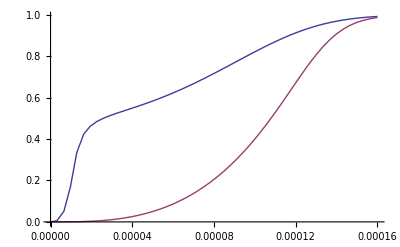

```mathematica
PrintTemporary[Dynamic[τ]];
Plot[{1/(p0∞)p[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0,τ},{.1,1}],1/(p1∞)p[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{0,τ},{1,∞}]},{τ,0,0.00016},MaxRecursion->0]
```

```mathematica
duration[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{.1,∞},part->0.5]
```

0.0000302649

```mathematica
duration[defaultUniverse[],{300,1.,1.,22.01039554696952,1.,0.00023951995459844163,-0.36664859506153297,-1.280471162683212},{defaultDetectorArea[],1.,0.011288050070583},{.1,∞}]
```

0.000157251

### Results

#### Sample Lightcurve

Paper

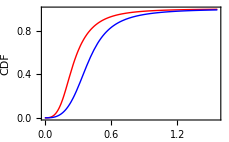

```mathematica
Block[{p1∞,p2∞,d},
p1∞=p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,∞},{0.1,1.}];
p2∞=p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,∞},{1.,∞}];
d=Max[duration[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0.1,1.}],duration[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{1.,∞}]];
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{1.,∞}]/(p2∞)
},{t,0,d},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","CDF"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",FontSize->10],Style["1 GeV - 300 GeV",FontSize->10]},{0.7,0.25}],LabelStyle->Directive[FontSize->10],ImageSize->230.1799598
]
]
```

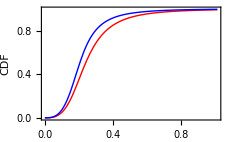

```mathematica
Block[{p1∞,p2∞,d},
p1∞=p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,∞},{0.1,1.}];
p2∞=p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,∞},{1.,∞}];
d=Max[duration[defaultUniverse[],defaultBurst[],defaultObserver[],{0.1,1.}],duration[defaultUniverse[],defaultBurst[],defaultObserver[],{1.,∞}]];
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[],{0,t},{1.,∞}]/(p2∞)
},{t,0,d},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","CDF"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",FontSize->10],Style["1 GeV - 300 GeV",FontSize->10]},{0.7,0.25}],LabelStyle->Directive[FontSize->10],ImageSize->230.1799598
]
]
```

Presentation

```mathematica
PrintTemporary[Dynamic[t]];
Plot[{
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{0.1,1.}]/(p1∞),
p[defaultUniverse[],defaultBurst[],defaultObserver[χ->0.01],{0,t},{1.,∞}]/(p2∞)
},{t,0,1},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, normalized","Photons Fraction"},FrameStyle->Gray,PlotLegends->Placed[{Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}],ImageSize->225
]
```

-Graphics-

#### Stretching Factors Histogram

```mathematica
κObserved={
{Text["090902B"],{0.363408,0.893437}},
{Text["090510"],{0.428137,1.60485}},
{Text["080916C"],{0.66529,3.31569}},
{Text["090926A"],{1.98759,6.61486}}
};
```

```mathematica
errorBar[{min_,max_},y_,height_,{label_,x_}]:=Graphics[{Black,Line[{{min,y},{max,y}}],Line[{{min,y-height},{min,y+height}}],Line[{{max,y-height},{max,y+height}}],{Black,Inset[label,{x,y},{Right,Bottom}]}}];
```

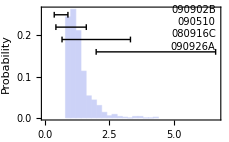

```mathematica
Block[{κ2,top},
κ2=Max[Transpose[Transpose[κObserved][[2]]][[2]]];
Show[
Histogram[mcData,Automatic,"Probability",PlotRangePadding->0,Frame->{{True,False},{True,False}},FrameLabel->{Style["Stretching Factor",FontSize->10],Style["Probability",FontSize->10]},PlotRange->{{0.,1.01κ2},All}],
Table[errorBar[κObserved[[it]][[2]],0.25-0.03(it-1),0.007,{Style[κObserved[[it]][[1]],FontSize->10],κ2}],{it,1,Length[κObserved]}],Axes->False,ImageSize->230.1799598
]
]
```

#### Stretching Factors CDF

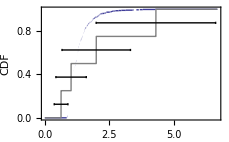

```mathematica
Block[{it,κ2},
κ2=Max[Transpose[Transpose[κObserved][[2]]][[2]]];
Show[
Plot[CDF[EmpiricalDistribution[mcData],κi],{κi,0.,1.01κ2},FrameLabel->{"Stretching Factor","CDF"},PlotRange->{{0,1.01κ2},All},Frame->{{True,False},{True,False}}],
Plot[CDF[EmpiricalDistribution[Table[Mean[value[[2]]],{value,κObserved}]],κi],{κi,0.,1.01κ2},PlotStyle->Gray],
Table[errorBar[κObserved[[it]][[2]],(2it-1)/(2Length[κObserved]),0.01,{"",κObserved[[it]][[2]][[1]]}],{it,1,Length[κObserved]}],Axes->False,ImageSize->230.1799598
]
]
```

```mathematica
Binomial[35,3] 0.072^3(1-0.072)^(35-3)
```

0.223585

#### Very High Energy Bursts Fraction

```mathematica
PrintTemporary[Dynamic[z]];
Timing[burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞}]]
```

{3321.83545,0.0720929}

```mathematica
PrintTemporary[Dynamic[z]];
Timing[burstFraction[defaultUniverse[],defaultPopulation[],defaultBurst500[],defaultDetectorArea[],{0.1,1.,∞}]]
```

{3738.33563,0.010223}